```mathematica
data={{1,1},{2,3},{−1,−3},{7,0},{4,−4}};
```

```mathematica
interpFunc=Interpolation[data,Method->"Spline"];
```

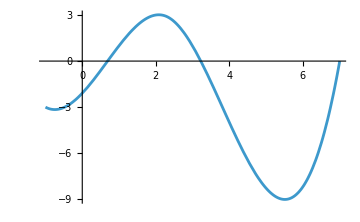

```mathematica
Plot[interpFunc[x],{x,-1,7}]
```

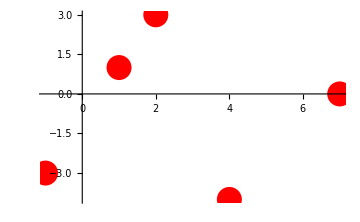

```mathematica
redDotPoint=ListPlot[data,PlotStyle->{Red,PointSize[0.05]}]
```

```mathematica
Manipulate[Show[Plot[interpFunc[x],{x,-1,t},PlotStyle->{Thick},PlotRange->All],redDotPoint],{t,-1.00001,7.000-0.0001,0.1}]
```